# Hierarchical Clustering

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Plot

```mathematica
data=({{1, 1}, {3, 2}, {1.5, 5}, {2, 6}, {3, 4}});
dataLabels=Subscript[bi["p"],#]&/@Range[Length[data]];
```

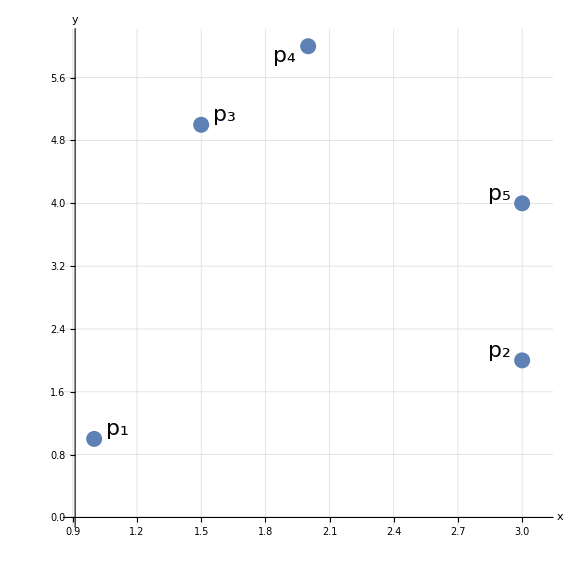

```mathematica
ListPlot[MapThread[Callout[#1,#2]&,{data,dataLabels}],
PlotTheme->{"myTheme"},
GridLines->Automatic,
AxesLabel->{it["x"],it["y"]},
AspectRatio->1,
PlotRange->{{0.9,3.1},{0,6.1}},
PlotStyle->Directive[PointSize[.02]]
]
```